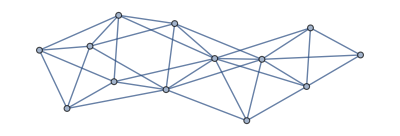

```mathematica
g=ReadGrof[10087]
```

```mathematica
e=CollectMPGEdges[g]
```

{1<->3,1<->12,2<->9,2<->12,3<->8,3<->13,4<->6,4<->8,4<->10,4<->13,5<->6,5<->7,5<->8,5<->10,6<->9,6<->10,6<->13,7<->11,8<->10,8<->13,9<->13,11<->12}

```mathematica
GraphWithChrom[g_]:=Labeled[If[PlanarGraphQ[g],Graph[g,GraphLayout->"PlanarEmbedding"],g],Style[{FindClique[g],Factor[ChromaticPolynomial[g,x]/(x(x-1))],ChromaticPolynomial[g,4]},If[ChromaticPolynomial[g,4]!=0,Darker[Green],Red],Underlined,If[PlanarGraphQ[g],Bold,Underlined]]]
```

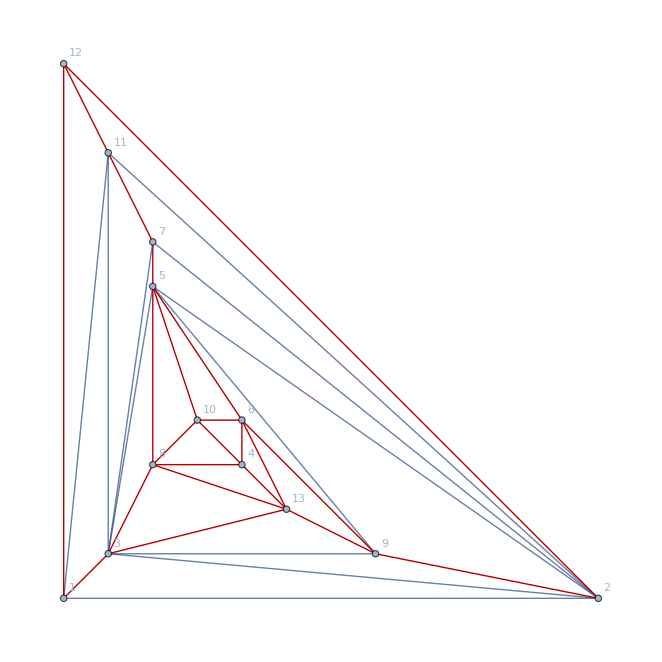

```mathematica
Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding",GraphHighlight->e]
```

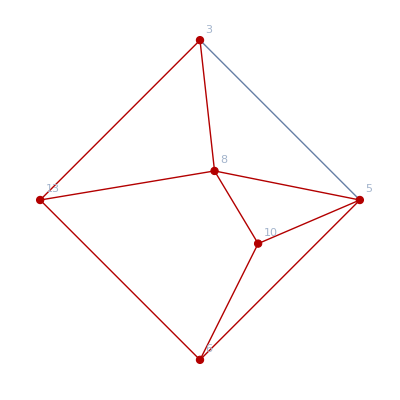
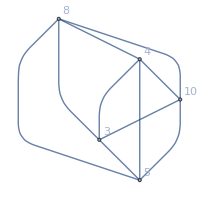
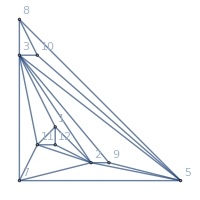
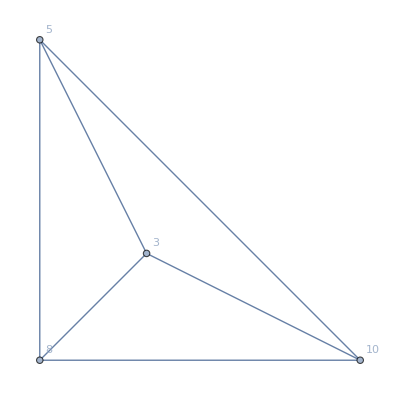
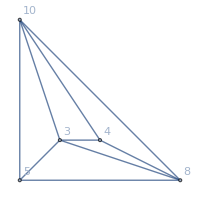
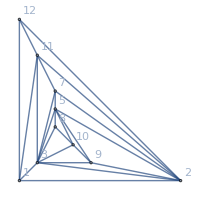
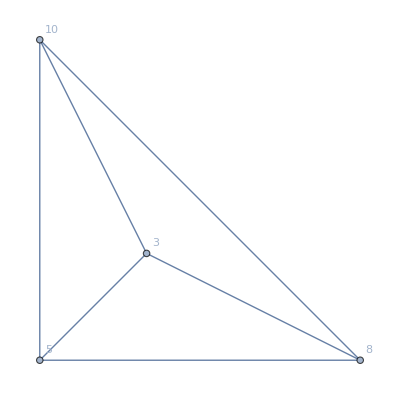
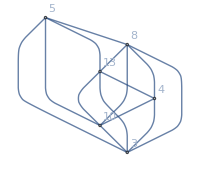
{10087,v,-Graphics-}→{{{{3,6},{5,13},{8},{10}},-Graphics-{{{8,4,10,3,5}},(-4+x) (-3+x) (-2+x),0},-Graphics-{{{1,2,11,12}},(-3+x)^6 (-2+x)^2,48},-Graphics-{{{8,10,3,5}},(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^6 (-2+x)^2 (-1+x) x,(-3+x) (-2+x) (-1+x) x,{},{v1789x2ax3cx5b,v179ax28x3cx5b},{v3x5x8xa}},{{{3,6},{5},{8},{10,13}},-Graphics-{{{5,8,3,10}},(-3+x)^2 (-2+x),24},-Graphics-{{{1,2,11,12}},(-3+x)^7 (-2+x),24},-Graphics-{{{5,8,3,10}},(-3+x) (-2+x),24},(-3+x)^2 (-2+x) (-1+x) x,(-3+x)^7 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{v3x45x8xa},{v1789x2ax3cx5b},{v3x5x8xa}},{{{3,6},{5},{8},{10},{13}},-Graphics-{{{5,8,13,10,3}},(-4+x)^2 (-3+x) (-2+x),0},-Graphics-{{{5,8,13,10,3}},(-4+x) (-3+x)^7 (-2+x),0},-Graphics-{{{5,8,13,10,3}},(-4+x) (-3+x) (-2+x),0},(-4+x)^2 (-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^7 (-2+x) (-1+x) x,(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}},{{{3,10},{5,13},{6,8}},-Graphics-{{{4,3,5,6}},(-3+x) (-2+x),24},-Graphics-{{{1,2,11,12}},(-3+x)^6 (-2+x),24},-Graphics-{{{3,5,6}},-2+x,24},(-3+x) (-2+x) (-1+x) x,(-3+x)^6 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v3x4x5x6},{v179x26x3cx5b},{v3x5x6}},{{{3,10},{5,13},{6},{8}},-Graphics-{{{8,4,6,3,5}},(-4+x) (-3+x) (-2+x),0},-Graphics-{{{1,2,11,12}},(-3+x)^7 (-2+x),24},-Graphics-{{{8,6,3,5}},(-3+x) (-2+x),24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^7 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{},{v1789x26x3cx5b},{v3x5x6x8}},{{{3,10},{5},{6,8},{13}},-Graphics-{{{5,13,3,6}},(-3+x)^2 (-2+x),24},-Graphics-{{{5,9,13,3,6}},(-4+x) (-3+x)^6 (-2+x),0},-Graphics-{{{5,13,3,6}},(-3+x) (-2+x),24},(-3+x)^2 (-2+x) (-1+x) x,(-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{v3x45x6xd},{},{v3x5x6xd}},{{{3,10},{5},{6},{8},{13}},-Graphics-{{{5,8,13,6,3}},(-4+x)^2 (-3+x) (-2+x),0},-Graphics-{{{5,9,13,6,3}},(-4+x)^2 (-3+x)^6 (-2+x),0},-Graphics-{{{5,8,13,6,3}},(-4+x) (-3+x) (-2+x),0},(-4+x)^2 (-3+x) (-2+x) (-1+x) x,(-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x,(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}},{{{3},{5,13},{6,8},{10}},-Graphics-{{{3,10,5,6}},(-3+x)^2 (-2+x),24},-Graphics-{{{1,2,3,11}},(-3+x)^7 (-2+x),24},-Graphics-{{{3,10,5,6}},(-3+x) (-2+x),24},(-3+x)^2 (-2+x) (-1+x) x,(-3+x)^7 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{v34x5x6xa},{v179ax26x3cx5b},{v3x5x6xa}},{{{3},{5,13},{6},{8},{10}},-Graphics-{{{3,8,6,10,5}},(-4+x)^2 (-3+x) (-2+x),0},-Graphics-{{{3,8,6,10,5}},(-4+x) (-3+x)^7 (-2+x),0},-Graphics-{{{3,8,6,10,5}},(-4+x) (-3+x) (-2+x),0},(-4+x)^2 (-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^7 (-2+x) (-1+x) x,(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}},{{{3},{5},{6,8},{10,13}},-Graphics-{{{3,5,6,10}},(-3+x) (-2+x)^2,48},-Graphics-{{{3,5,9,6,10}},(-4+x) (-3+x)^6 (-2+x),0},-Graphics-{{{3,5,6,10}},(-3+x) (-2+x),24},(-3+x) (-2+x)^2 (-1+x) x,(-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{v3x45x6xa,v34x5x6xa},{},{v3x5x6xa}},{{{3},{5},{6,8},{10},{13}},-Graphics-{{{3,5,13,10,6}},(-4+x) (-3+x)^2 (-2+x),0},-Graphics-{{{3,5,9,13,6}},(-4+x)^2 (-3+x)^6 (-2+x),0},-Graphics-{{{3,5,13,10,6}},(-4+x) (-3+x) (-2+x),0},(-4+x) (-3+x)^2 (-2+x) (-1+x) x,(-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x,(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}},{{{3},{5},{6},{8},{10,13}},-Graphics-{{{3,5,8,6,10}},(-4+x) (-3+x)^2 (-2+x),0},-Graphics-{{{3,5,9,6,10}},(-4+x)^2 (-3+x)^6 (-2+x),0},-Graphics-{{{3,5,8,6,10}},(-4+x) (-3+x) (-2+x),0},(-4+x) (-3+x)^2 (-2+x) (-1+x) x,(-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x,(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}},{{{3},{5},{6},{8},{10},{13}},-Graphics-{{{3,5,8,13,6,10}},(-5+x) (-4+x)^2 (-3+x) (-2+x),0},-Graphics-{{{3,5,8,13,6,10}},(-5+x) (-4+x)^2 (-3+x)^6 (-2+x),0},-Graphics-{{{3,5,8,13,6,10}},(-5+x) (-4+x) (-3+x) (-2+x),0},(-5+x) (-4+x)^2 (-3+x) (-2+x) (-1+x) x,(-5+x) (-4+x)^2 (-3+x)^6 (-2+x) (-1+x) x,(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}}}{(-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),{3,13,6,5,10,8},13,{v1789x2adx36cx45b,v179ax268x34cx5bd,v1479x268x3acx5bd}}

```mathematica
With[{k=10087},
Block[{g=ReadGrof[k],adj},
adj={3,13,6,5,10,8};
{Style[k,If[OddQ[k],Blue,Purple]],v,Subgraph[Graph[g,GraphHighlight->Join[adj,CollectMPGEdges[g]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",VertexStyle->{v->Green},VertexSize->{v->Large}],Append[adj,v],GraphLayout->"TutteEmbedding"]}->Labeled[ZykovDecomposition23[g,adj],Style[{Factor[ChromaticPolynomial[g,x]],adj,ZykovSolutionCount[g,adj],FindFullFormula1234[g]},Bold,24]]
]
]
```

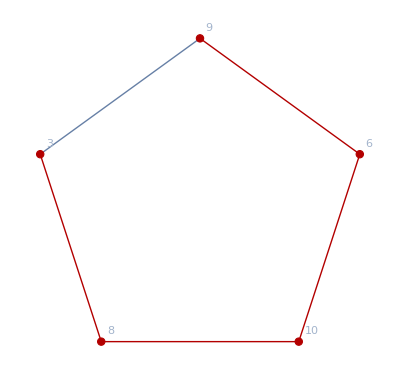
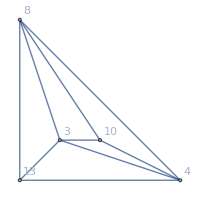
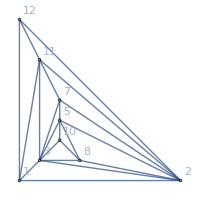
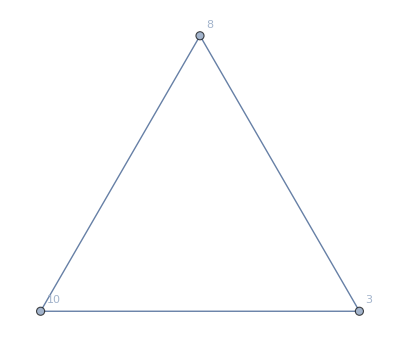
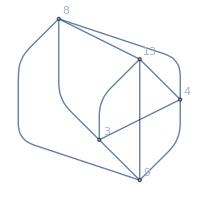
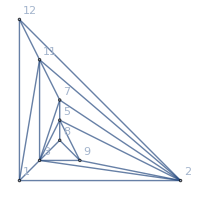
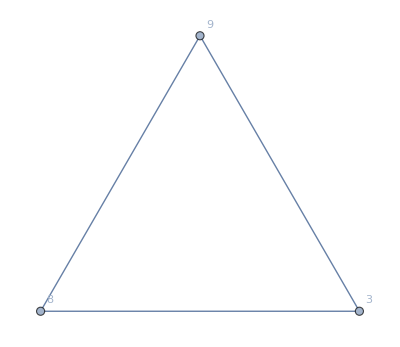
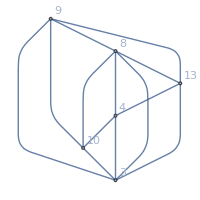
{10087,v,-Graphics-}→{{{{3,6},{8,9},{10}},-Graphics-{{{13,4,3,8}},(-3+x)^2 (-2+x),24},-Graphics-{{{1,2,11,12}},(-3+x)^6 (-2+x),24},-Graphics-{{{10,3,8}},-2+x,24},(-3+x)^2 (-2+x) (-1+x) x,(-3+x)^6 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v3x4x8xad},{v178x2ax3cx5b},{v3x8xa}},{{{3,6},{8},{9,10}},-Graphics-{{{8,13,4,3,9}},(-4+x) (-3+x) (-2+x),0},-Graphics-{{{1,2,11,12}},(-3+x)^6 (-2+x),24},-Graphics-{{{8,3,9}},-2+x,24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^6 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{},{v179x28x3cx5b},{v3x8x9}},{{{3,6},{8},{9},{10}},-Graphics-{{{9,8,13,3}},(-3+x) (-2+x) (13-7 x+x^2),24},-Graphics-{{{5,9,8,10,3}},(-4+x) (-3+x)^6 (-2+x),0},-Graphics-{{{9,8,10,3}},(-3+x) (-2+x),24},(-3+x) (-2+x) (-1+x) x (13-7 x+x^2),(-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{v3x49x8xad},{},{v3x8x9xa}},{{{3,10},{6},{8,9}},-Graphics-{{{13,4,6,3,8}},(-4+x) (-3+x) (-2+x),0},-Graphics-{{{1,2,11,12}},(-3+x)^6 (-2+x),24},-Graphics-{{{6,3,8}},-2+x,24},(-4+x) (-3+x) (-2+x) (-1+x) x,(-3+x)^6 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{},{v178x26x3cx5b},{v3x6x8}},{{{3,10},{6,8},{9}},-Graphics-{{{9,13,3,6}},(-3+x)^2 (-2+x),24},-Graphics-{{{1,2,11,12}},(-3+x)^6 (-2+x),24},-Graphics-{{{9,3,6}},-2+x,24},(-3+x)^2 (-2+x) (-1+x) x,(-3+x)^6 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v3x49x6xd},{v179x26x3cx5b},{v3x6x9}},{{{3,10},{6},{8},{9}},-Graphics-{{{9,8,13,6,3}},(-4+x)^2 (-3+x) (-2+x),0},-Graphics-{{{5,9,8,6,3}},(-4+x) (-3+x)^6 (-2+x),0},-Graphics-{{{9,8,6,3}},(-3+x) (-2+x),24},(-4+x)^2 (-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{},{},{v3x6x8x9}},{{{3},{6},{8,9},{10}},-Graphics-{{{3,13,6,8}},(-3+x) (-2+x) (13-7 x+x^2),24},-Graphics-{{{3,5,6,10,8}},(-4+x) (-3+x)^6 (-2+x),0},-Graphics-{{{3,6,10,8}},(-3+x) (-2+x),24},(-3+x) (-2+x) (-1+x) x (13-7 x+x^2),(-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{v34x6x8xad},{},{v3x6x8xa}},{{{3},{6,8},{9,10}},-Graphics-{{{3,13,6,9}},(-3+x)^2 (-2+x),24},-Graphics-{{{1,2,3,11}},(-3+x)^6 (-2+x),24},-Graphics-{{{3,6,9}},-2+x,24},(-3+x)^2 (-2+x) (-1+x) x,(-3+x)^6 (-2+x) (-1+x) x,(-2+x) (-1+x) x,{v34x6x9xd},{v179x26x3cx5b},{v3x6x9}},{{{3},{6},{8},{9,10}},-Graphics-{{{3,8,13,6,9}},(-4+x)^2 (-3+x) (-2+x),0},-Graphics-{{{3,5,8,6,9}},(-4+x) (-3+x)^6 (-2+x),0},-Graphics-{{{3,8,6,9}},(-3+x) (-2+x),24},(-4+x)^2 (-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{},{},{v3x6x8x9}},{{{3},{6,8},{9},{10}},-Graphics-{{{3,9,13,6}},(-3+x) (-2+x) (10-6 x+x^2),48},-Graphics-{{{3,5,9,10,6}},(-4+x) (-3+x)^6 (-2+x),0},-Graphics-{{{3,9,10,6}},(-3+x) (-2+x),24},(-3+x) (-2+x) (-1+x) x (10-6 x+x^2),(-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,{v3x49x6xad,v34x6x9xad},{},{v3x6x9xa}},{{{3},{6},{8},{9},{10}},-Graphics-{{{3,9,8,13,6}},(-4+x) (-3+x) (-2+x) (17-8 x+x^2),0},-Graphics-{{{3,5,9,8,6,10}},(-5+x) (-4+x) (-3+x)^6 (-2+x),0},-Graphics-{{{3,9,8,6,10}},(-4+x) (-3+x) (-2+x),0},(-4+x) (-3+x) (-2+x) (-1+x) x (17-8 x+x^2),(-5+x) (-4+x) (-3+x)^6 (-2+x) (-1+x) x,(-4+x) (-3+x) (-2+x) (-1+x) x,{},{},{}}}{(-3+x)^6 (-2+x) (-1+x) x (119-133 x+58 x^2-12 x^3+x^4),{9,6,10,8,3},11,{v1789x2adx36cx45b,v179ax268x34cx5bd,v1479x268x3acx5bd}}

```mathematica
With[{k=10087},
Block[{g=ReadGrof[k],adj},
adj={9,6,10,8,3};
{Style[k,If[OddQ[k],Blue,Purple]],v,Subgraph[Graph[g,GraphHighlight->Join[adj,CollectMPGEdges[g]],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",VertexStyle->{v->Green},VertexSize->{v->Large}],Append[adj,v],GraphLayout->"TutteEmbedding"]}->Labeled[ZykovDecomposition23[g,adj],Style[{Factor[ChromaticPolynomial[g,x]],adj,ZykovSolutionCount[g,adj],FindFullFormula1234[g]},Bold,24]]
]
]
```